## Energy Function - evolution w.r.t. coordinates θ,φ

```mathematica
IF[X_]:=1/(2*X);
I1=72;I2=15;I3=7;V=2.1;γ=22;j=13/2;
m1={π/2,0};m2={π/2,π};m3={π/2,2π};
Hen[I_,θ_,φ_,A1_,A2_,A3_,V_,γ_]:=I/2(A1+A2)+A3*I^2+I(I-1/2)Sin[θ]^2(A1*Cos[φ]^2+A2*Sin[φ]^2-A3)+j/2(A2+A3)+A1*j^2-2A1*I*j*Sin[θ]-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
```

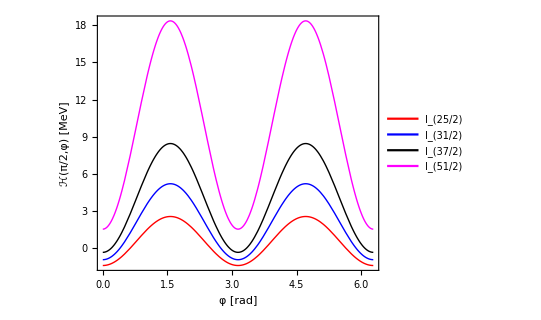

```mathematica
Plot[{Hen[25/2,m1[[1]],y,IF[I1],IF[I2],IF[I3],V,γ],Hen[31/2,m1[[1]],y,IF[I1],IF[I2],IF[I3],V,γ],Hen[37/2,m1[[1]],y,IF[I1],IF[I2],IF[I3],V,γ],Hen[51/2,m1[[1]],y,IF[I1],IF[I2],IF[I3],V,γ]},{y,0,2π},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Magenta,Thick}},FrameLabel->{"φ [rad]","ℋ(π/2,φ) [MeV]"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[{"I_(25/2)","I_(31/2)","I_(37/2)","I_(51/2)"},{0.5,0.7}]]
```

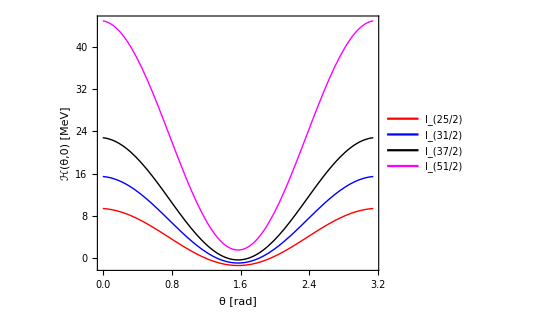

```mathematica
Plot[{Hen[25/2,x,m1[[2]],IF[I1],IF[I2],IF[I3],V,γ],Hen[31/2,x,m1[[2]],IF[I1],IF[I2],IF[I3],V,γ],Hen[37/2,x,m1[[2]],IF[I1],IF[I2],IF[I3],V,γ],Hen[51/2,x,m1[[2]],IF[I1],IF[I2],IF[I3],V,γ]},{x,0,π},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Magenta,Thick}},FrameLabel->{"θ [rad]","ℋ(θ,0) [MeV]"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[{"I_(25/2)","I_(31/2)","I_(37/2)","I_(51/2)"},{0.5,0.7}]]
```